```mathematica
(************************Program Mahdi Molavi************************)
(********* git hub : https://github.com/mahdipc/mathematica*************)
```

```mathematica
Remove["Global`*"];
Clear["Global`*"];
ν[Ι_,V_]:=Module[{i=Ι,v=V},
sol=Sort[v/.N[Solve[ChebyshevT[n+1,v]==0,v,Reals]],Less];
Return[sol[[i]]];
];
𝓉[Ι_]:=Module[{i=Ι+1},
If[i==1,Return[0]];
If[i== n+1,Return[1]];
Return[1/2((2 ν[i,v]-(ν[n+1,v]+ν[1,v]))/(ν[n+1,v]-ν[1,v])+1)];
];
χ[Ι_,V_]:=Module[{i=Ι,v=V},
sol=Sort[v/.N[Solve[ChebyshevT[k+1,v]==0,v,Reals]],Less];
Return[sol[[i]]];
];
τ[Ι_]:=Module[{i=Ι+1},
If[i== 1,Return[0];];
If[i==k+1,Return[1];];
Return[1/2((2 χ[i,v]-(χ[k+1,v]+χ[1,v]))/(χ[k+1,v]-χ[1,v])+1)];
];
𝓉[J_,Ι_]:=Module[{i=Ι,j=J},
(*If[j==1&&i==0,Return[0];];*)
If[0≤ j≤ k && 1≤ i≤ n,
h=𝓉[i]-𝓉[i-1];
Return[𝓉[i-1]+τ[j] h];
, 
Print["ERROR:    i=",i,"   j=",j];
];
];
ϕ[J_,T_]:=Module[{j=J,t=T},
Return[Product[If[l≠ j,t-τ[l],1],{l,0,k}]/Product[If[l≠ j,τ[j]-τ[l],1],{l,0,k}]];
];
R[Ι_,J_,T_]:=Module[{i=Ι,j=J,t=T},
Return[Product[If[l≠ j,(t-𝓉[l,i]),1],{l,0,k}]/(t-𝓉[j,i])];
];
ϕ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
(*
If[j==0 && i==1,
(*Return[Piecewise[{{R[1,0,t]/R[1,0,𝓉[1,0]],𝓉[0]≤ t≤ 𝓉[1]}},0]];*)
Return[Piecewise[{{ϕ[0,(t-𝓉[0])/(𝓉[1]-𝓉[0])],𝓉[0]≤ t≤ 𝓉[1]}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,Return[Piecewise[{{R[i,j,t]/R[i,j,𝓉[i,j]],𝓉[i-1]≤ t≤ 𝓉[i]}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{{∏_(l=0)^(k-1) (t-𝓉[l,i])/(𝓉[k,i]-𝓉[l,i]),𝓉[i-1]≤ t≤ 𝓉[i]},
{∏_(l=1)^k (t-𝓉[l,i+1])/(𝓉[0,i+1]-𝓉[l,i+1]),𝓉[i]≤ t≤ 𝓉[i+1]}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{ϕ[k,(t-𝓉[n-1])/(𝓉[n]-𝓉[n-1])],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];
(*Return[Piecewise[{{R[n,k,t]/R[n,k,𝓉[k,n]],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];*)
];
*)
If[j==0 && i==1,
Return[Piecewise[{{ϕ[0,(t-𝓉[0])/(𝓉[1]-𝓉[0])],𝓉[0]≤ t≤ 𝓉[1]}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,
Return[Piecewise[{{ϕ[j,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{ϕ[k,(t-𝓉[n-1])/(𝓉[n]-𝓉[n-1])],𝓉[n-1]≤ t≤ 𝓉[n]}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{
{ϕ[k,(t-𝓉[i-1])/(𝓉[i]-𝓉[i-1])],𝓉[i-1]≤ t≤ 𝓉[i]},
{ϕ[0,(t-𝓉[i])/(𝓉[i+1]-𝓉[i])],𝓉[i]≤ t≤ 𝓉[i+1]}},
0]];
];
];
ψ[J_,Ι_,T_]:=Module[{i=Ι,j=J,t=T},
If[j==0&& i==1,
Return[Piecewise[{{1,0≤ t≤ 𝓉[1,1]/2}},0]];
];
If[1≤ j≤ k-1 && 1≤ i≤ n,
Return[Piecewise[{{1,(𝓉[j-1,i]+𝓉[j,i])/2≤ t≤ (𝓉[j,i]+𝓉[j+1,i])/2}},0]];
];
If[j==k && 1≤ i≤ n-1,
Return[Piecewise[{{1,(𝓉[k-1,i]+𝓉[k,i])/2≤ t≤ (𝓉[0,i+1]+𝓉[1,i+1])/2}},0]];
];
If[j==k && i==n,
Return[Piecewise[{{1,(𝓉[k-1,n]+𝓉[k,n])/2≤ t≤ 1}},0]];
];
];
ψ[J_,T_]:=Module[{j=J,t=T},
If[j==0,Return[Piecewise[{{1,0≤ t≤ (τ[0]+τ[1])/2}},0]]];
If[j==k,Return[Piecewise[{{1,(τ[k]+τ[k-1])/2≤ t≤ 1}},0]]];
Return[Piecewise[{{1,(τ[j]+τ[j-1])/2≤ t≤(τ[j]+τ[j+1])/2}},0]];
];
b[Ι_,J_,T_]:=Module[{i=Ι,j=J,t=T},
Return[∫_0^1 ϕ[i,t]ψ[j,t]ⅆt];
];
(*****************************)
AK[s_,t_]=(ⅇ^t Sin[t])/(1+s^2);
AF[t_]=t^3+1/2 ⅇ^t(-1+Log[2])Sin[t];
Ax[t_]=t^3;
k=5;
n=5;
(*****************************)
Ν=n k+1;
d[t_]=Simplify[Join[{ψ[0,1,t]},Flatten[Table[ψ[j,i,t],{j,1,k},{i,1,n}]]]];
b[t_]=Simplify[Join[{ϕ[0,1,t]},Flatten[Table[ϕ[j,i,t],{j,1,k},{i,1,n}]]]];
VC=Table[Subscript[c, i],{i,1,Ν}];
(*B=Table[NIntegrate[b[t]⟦i⟧d[t]⟦j⟧,{t,0,1},PrecisionGoal->12,MaxRecursion->120],{i,1,Ν},{j,1,Ν}]*)
```

```mathematica
B=ParallelTable[N[∫_0^1 b[t]⟦i⟧d[t]⟦j⟧ⅆt],{i,1,Ν},{j,1,Ν}]
```

{{0.00555366,0.0000293216,0.,0.,0.,0.,-0.000148842,0.,0.,0.,0.,0.000174851,0.,0.,0.,0.,-0.000182998,0.,0.,0.,0.,0.000158204,0.,0.,0.,0.},{0.0045528,0.0211386,0.,0.,0.,0.,0.00148808,0.,0.,0.,0.,-0.000707517,0.,0.,0.,0.,0.000611584,0.,0.,0.,0.,-0.000502373,0.,0.,0.,0.},{0.,0.,0.0366131,0.,0.,0.,0.,0.00257743,0.,0.,0.,0.,-0.00122546,0.,0.,0.,0.,0.00105929,0.,0.,0.,0.00788568,-0.000870136,0.,0.,0.},{0.,0.,0.,0.0422772,0.,0.,0.,0.,0.00297616,0.,0.,0.,0.,-0.00141503,0.,0.,0.,0.,0.00122317,0.,0.,0.,0.0091056,-0.00100475,0.,0.},{0.,0.,0.,0.,0.0366131,0.,0.,0.,0.,0.00257743,0.,0.,0.,0.,-0.00122546,0.,0.,0.,0.,0.00105929,0.,0.,0.,0.00788568,-0.000870136,0.},{0.,0.,0.,0.,0.,0.0211386,0.,0.,0.,0.,0.00148808,0.,0.,0.,0.,-0.000707517,0.,0.,0.,0.,0.000611584,0.,0.,0.,0.0045528,-0.000502373},{-0.00174239,0.00427467,0.,0.,0.,0.,0.0295733,0.,0.,0.,0.,0.00311376,0.,0.,0.,0.,-0.00135211,0.,0.,0.,0.,0.000954701,0.,0.,0.,0.},{0.,0.,0.00740394,0.,0.,0.,0.,0.0512225,0.,0.,0.,0.,0.00539319,0.,0.,0.,0.,-0.00234193,0.,0.,0.,-0.00301791,0.00165359,0.,0.,0.},{0.,0.,0.,0.00854933,0.,0.,0.,0.,0.0591466,0.,0.,0.,0.,0.00622752,0.,0.,0.,0.,-0.00270423,0.,0.,0.,-0.00348478,0.0019094,0.,0.},{0.,0.,0.,0.,0.00740394,0.,0.,0.,0.,0.0512225,0.,0.,0.,0.,0.00539319,0.,0.,0.,0.,-0.00234193,0.,0.,0.,-0.00301791,0.00165359,0.},{0.,0.,0.,0.,0.,0.00427467,0.,0.,0.,0.,0.0295733,0.,0.,0.,0.,0.00311376,0.,0.,0.,0.,-0.00135211,0.,0.,0.,-0.00174239,0.000954701},{0.000954701,-0.00135211,0.,0.,0.,0.,0.00311376,0.,0.,0.,0.,0.0295733,0.,0.,0.,0.,0.00427467,0.,0.,0.,0.,-0.00174239,0.,0.,0.,0.},{0.,0.,-0.00234193,0.,0.,0.,0.,0.00539319,0.,0.,0.,0.,0.0512225,0.,0.,0.,0.,0.00740394,0.,0.,0.,0.00165359,-0.00301791,0.,0.,0.},{0.,0.,0.,-0.00270423,0.,0.,0.,0.,0.00622752,0.,0.,0.,0.,0.0591466,0.,0.,0.,0.,0.00854933,0.,0.,0.,0.0019094,-0.00348478,0.,0.},{0.,0.,0.,0.,-0.00234193,0.,0.,0.,0.,0.00539319,0.,0.,0.,0.,0.0512225,0.,0.,0.,0.,0.00740394,0.,0.,0.,0.00165359,-0.00301791,0.},{0.,0.,0.,0.,0.,-0.00135211,0.,0.,0.,0.,0.00311376,0.,0.,0.,0.,0.0295733,0.,0.,0.,0.,0.00427467,0.,0.,0.,0.000954701,-0.00174239},{-0.000502373,0.000611584,0.,0.,0.,0.,-0.000707517,0.,0.,0.,0.,0.00148808,0.,0.,0.,0.,0.0211386,0.,0.,0.,0.,0.0045528,0.,0.,0.,0.},{0.,0.,0.00105929,0.,0.,0.,0.,-0.00122546,0.,0.,0.,0.,0.00257743,0.,0.,0.,0.,0.0366131,0.,0.,0.,-0.000870136,0.00788568,0.,0.,0.},{0.,0.,0.,0.00122317,0.,0.,0.,0.,-0.00141503,0.,0.,0.,0.,0.00297616,0.,0.,0.,0.,0.0422772,0.,0.,0.,-0.00100475,0.0091056,0.,0.},{0.,0.,0.,0.,0.00105929,0.,0.,0.,0.,-0.00122546,0.,0.,0.,0.,0.00257743,0.,0.,0.,0.,0.0366131,0.,0.,0.,-0.000870136,0.00788568,0.},{0.,0.,0.,0.,0.,0.000611584,0.,0.,0.,0.,-0.000707517,0.,0.,0.,0.,0.00148808,0.,0.,0.,0.,0.0211386,0.,0.,0.,-0.000502373,0.0045528},{0.000158204,-0.000182998,0.0000507865,0.,0.,0.,0.000174851,-0.000257802,0.,0.,0.,-0.000148842,0.00030285,0.,0.,0.,0.0000293216,-0.000316962,0.,0.,0.,0.0151729,0.000274017,0.,0.,0.},{0.,0.,-0.000316962,0.0000586432,0.,0.,0.,0.00030285,-0.000297684,0.,0.,0.,-0.000257802,0.000349701,0.,0.,0.,0.0000507865,-0.000365996,0.,0.,0.000274017,0.0207265,0.000316407,0.,0.},{0.,0.,0.,-0.000365996,0.0000507865,0.,0.,0.,0.000349701,-0.000257802,0.,0.,0.,-0.000297684,0.00030285,0.,0.,0.,0.0000586432,-0.000316962,0.,0.,0.000316407,0.0207265,0.000274017,0.},{0.,0.,0.,0.,-0.000316962,0.0000293216,0.,0.,0.,0.00030285,-0.000148842,0.,0.,0.,-0.000257802,0.000174851,0.,0.,0.,0.0000507865,-0.000182998,0.,0.,0.000274017,0.0151729,0.000158204},{0.,0.,0.,0.,0.,-0.000182998,0.,0.,0.,0.,0.000174851,0.,0.,0.,0.,-0.000148842,0.,0.,0.,0.,0.0000293216,0.,0.,0.,0.000158204,0.00555366}}

```mathematica
K=ParallelTable[N[∫_0^1 ∫_0^1 AK[t,s]b[t]⟦i⟧d[t]⟦j⟧ⅆs ⅆt ],{i,1,Ν},{j,1,Ν}]
```

{{0.00505001,0.0000273045,0.,0.,0.,0.,-0.000136241,0.,0.,0.,0.,0.000159097,0.,0.,0.,0.,-0.000164912,0.,0.,0.,0.,0.000141519,0.,0.,0.,0.},{0.00413984,0.0192132,0.,0.,0.,0.,0.00135545,0.,0.,0.,0.,-0.00064314,0.,0.,0.,0.,0.000551094,0.,0.,0.,0.,-0.000449392,0.,0.,0.,0.},{0.,0.,0.0323651,0.,0.,0.,0.,0.00230555,0.,0.,0.,0.,-0.00107134,0.,0.,0.,0.,0.000883331,0.,0.,0.,0.00702509,-0.000701938,0.,0.,0.},{0.,0.,0.,0.0329905,0.,0.,0.,0.,0.00237264,0.,0.,0.,0.,-0.00106933,0.,0.,0.,0.,0.000847147,0.,0.,0.,0.00724711,-0.000658083,0.,0.},{0.,0.,0.,0.,0.023,0.,0.,0.,0.,0.00165434,0.,0.,0.,0.,-0.000740997,0.,0.,0.,0.,0.000586378,0.,0.,0.,0.00506895,-0.000456342,0.},{0.,0.,0.,0.,0.,0.0107661,0.,0.,0.,0.,0.000768058,0.,0.,0.,0.,-0.000352026,0.,0.,0.,0.,0.000288596,0.,0.,0.,0.0023523,-0.000229649},{-0.00158435,0.00388307,0.,0.,0.,0.,0.026823,0.,0.,0.,0.,0.00282393,0.,0.,0.,0.,-0.00121811,0.,0.,0.,0.,0.000854021,0.,0.,0.,0.},{0.,0.,0.0064943,0.,0.,0.,0.,0.044413,0.,0.,0.,0.,0.00465848,0.,0.,0.,0.,-0.00195092,0.,0.,0.,-0.00268891,0.00133398,0.,0.,0.},{0.,0.,0.,0.00654612,0.,0.,0.,0.,0.0441934,0.,0.,0.,0.,0.00460501,0.,0.,0.,0.,-0.00186972,0.,0.,0.,-0.00277453,0.00125065,0.,0.},{0.,0.,0.,0.,0.00455124,0.,0.,0.,0.,0.0306681,0.,0.,0.,0.,0.00319041,0.,0.,0.,0.,-0.00129425,0.,0.,0.,-0.00194077,0.00086725,0.},{0.,0.,0.,0.,0.,0.00214817,0.,0.,0.,0.,0.0146249,0.,0.,0.,0.,0.00152874,0.,0.,0.,0.,-0.000637412,0.,0.,0.,-0.000900491,0.000436428},{0.000868109,-0.00122813,0.,0.,0.,0.,0.0028163,0.,0.,0.,0.,0.0267008,0.,0.,0.,0.,0.00384871,0.,0.,0.,0.,-0.00155866,0.,0.,0.,0.},{0.,0.,-0.00205114,0.,0.,0.,0.,0.00458253,0.,0.,0.,0.,0.0431922,0.,0.,0.,0.,0.00615118,0.,0.,0.,0.00147336,-0.00243473,0.,0.,0.},{0.,0.,0.,-0.00206286,0.,0.,0.,0.,0.00445842,0.,0.,0.,0.,0.0418398,0.,0.,0.,0.,0.00588448,0.,0.,0.,0.00152034,-0.00228272,0.,0.},{0.,0.,0.,0.,-0.00143339,0.,0.,0.,0.,0.00308442,0.,0.,0.,0.,0.0289709,0.,0.,0.,0.,0.00407389,0.,0.,0.,0.00106348,-0.00158292,0.},{0.,0.,0.,0.,0.,-0.000677681,0.,0.,0.,0.,0.00149803,0.,0.,0.,0.,0.0141336,0.,0.,0.,0.,0.00200994,0.,0.,0.,0.000493427,-0.00079655},{-0.000456808,0.000555481,0.,0.,0.,0.,-0.000639053,0.,0.,0.,0.,0.00133359,0.,0.,0.,0.,0.0189756,0.,0.,0.,0.,0.00407301,0.,0.,0.,0.},{0.,0.,0.000927237,0.,0.,0.,0.,-0.00103061,0.,0.,0.,0.,0.00208743,0.,0.,0.,0.,0.0300039,0.,0.,0.,-0.000775304,0.00636376,0.,0.,0.},{0.,0.,0.,0.000931741,0.,0.,0.,0.,-0.000990731,0.,0.,0.,0.,0.00195194,0.,0.,0.,0.,0.0284294,0.,0.,0.,-0.000800036,0.0059676,0.,0.},{0.,0.,0.,0.,0.000647282,0.,0.,0.,0.,-0.000684209,0.,0.,0.,0.,0.00135061,0.,0.,0.,0.,0.0196949,0.,0.,0.,-0.000559629,0.00413806,0.},{0.,0.,0.,0.,0.,0.000306217,0.,0.,0.,0.,-0.000335573,0.,0.,0.,0.,0.000680086,0.,0.,0.,0.,0.00980757,0.,0.,0.,-0.00025965,0.00208193},{0.000143855,-0.000166209,0.0000606972,0.,0.,0.,0.000157839,-0.000238673,0.,0.,0.,-0.000132274,0.000266117,0.,0.,0.,0.0000226336,-0.00026441,0.,0.,0.,0.0135438,0.000221048,0.,0.,0.},{0.,0.,-0.00027739,0.000085385,0.,0.,0.,0.000253573,-0.000254208,0.,0.,0.,-0.000199096,0.000266689,0.,0.,0.,0.0000148609,-0.000253642,0.,0.,0.000244154,0.0166095,0.000207236,0.,0.},{0.,0.,0.,-0.000278649,0.0000636467,0.,0.,0.,0.000242487,-0.000178058,0.,0.,0.,-0.000177869,0.000184819,0.,0.,0.,-3.57258×10^-6,-0.000175563,0.,0.,0.000251944,0.0134559,0.000143706,0.},{0.,0.,0.,0.,-0.000193562,0.00002415,0.,0.,0.,0.000167335,-0.0000804633,0.,0.,0.,-0.000122939,0.0000874888,0.,0.,0.,-1.56579×10^-6,-0.0000863848,0.,0.,0.000176236,0.00790516,0.0000723189},{0.,0.,0.,0.,0.,-0.0000915923,0.,0.,0.,0.,0.0000824236,0.,0.,0.,0.,-0.0000644984,0.,0.,0.,0.,5.15655×10^-6,0.,0.,0.,0.0000817677,0.00253433}}

```mathematica
F=ParallelTable[N[∫_0^1 AF[t]d[t]⟦i⟧ⅆt],{i,1,Ν}]
```

{-6.21417×10^-6,-0.0000814677,-0.00109979,-0.00114395,0.00490665,0.0100458,-0.00026715,-0.00179966,-0.000539797,0.00969117,0.015581,-0.000447399,-0.00196967,0.00129507,0.0138311,0.0178992,-0.000438383,-0.00140743,0.00258418,0.0132203,0.0146862,-0.000526765,-0.00100215,0.00276934,0.0089764,0.0057281}

```mathematica
VC=Inverse[(B-K)].F
(*ANS=(B-K).VC-F;
VC=Flatten[VC/.Solve[ANS==0,VC]]*)
```

{-0.00287488,-0.0470416,-0.191429,-0.0551375,0.301551,0.708304,-0.0687235,-0.227236,-0.0621325,0.362983,0.873692,-0.152948,-0.217607,0.0961008,0.593493,1.05366,-0.121878,-0.146201,0.0919803,0.479109,0.84595,-0.319585,-0.252203,0.36651,1.22012,1.88362}

```mathematica
x[t_]=Simplify[∑_(i=1)^Ν VC⟦i⟧b[t]⟦i⟧]
```

Piecewise[{{0., t>1.||t<0}, {-1.3035×10^6+7.05122×10^6 t-1.52628×10^7 t^2+1.65277×10^7 t^3-8.95559×10^6 t^4+1.94305×10^6 t^5, t==0.866025}, {-496639.+2.75731×10^6 t-6.11346×10^6 t^2+6.76673×10^6 t^3-3.73924×10^6 t^4+825297. t^5, 0.866025<t≤1.}, {-13732.8+95146.4 t-262796. t^2+361702. t^3-248077. t^4+67830.6 t^5, 0.633975<t<0.866025}, {-19808.4+137154. t-381799. t^2+535707. t^3-380298. t^4+109772. t^5, t==0.633975}, {-612.221+6346.73 t-26119.2 t^2+53324.3 t^3-54004.3 t^4+21709.2 t^5, 0.366025≤t<0.633975}, {15.4692-338.27 t+3234.42 t^2-22937.8 t^3+134364. t^4-385832. t^5, t==0.133975}, {-0.00287488-7.86707 t+474.402 t^2-11524.3 t^3+111055. t^4-367073. t^5, 0≤t<0.133975}, {-6.49493+106.776 t-639.048 t^2+1514.92 t^3-789.518 t^4-1117.5 t^5, True}}]

0.0179492

{{0.0470473,0.0688415,0.15356,0.12344,0.32199},{0.195926,0.237727,0.239816,0.183775,0.301241},{0.120065,0.162095,0.0578023,0.121949,-0.111701},{-0.00738681,0.0085737,-0.116951,0.102941,-0.570606},{-0.0175564,-0.107472,-0.193679,0.101163,-0.883618}}

0.883618

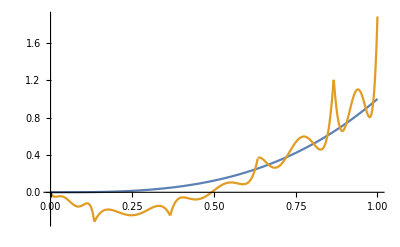

```mathematica
𝓉[1,1]
Table[Ax[𝓉[j,i]]-x[𝓉[j,i]],{i,1,n},{j,1,k}]
Norm[Flatten[Table[Ax[𝓉[i]]-x[𝓉[i]],{i,1,n}]],Infinity]
Plot[{Ax[t],x[t]},{t,0,1}]
```

```mathematica
Table[𝓉[j,i],{i,n},{j,k}]
```

{{0.0179492,0.0490381,0.0849365,0.116025,0.133975},{0.165064,0.218911,0.281089,0.334936,0.366025},{0.401924,0.464102,0.535898,0.598076,0.633975},{0.665064,0.718911,0.781089,0.834936,0.866025},{0.883975,0.915064,0.950962,0.982051,1.}}